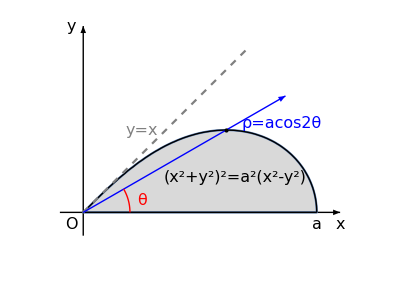

```mathematica
tF={FontFamily->"Times",FontSize->16};(* 字体设置：16pt, Times *)
(********绘图区+坐标系*******)
f1={
Graphics[{{White,Rectangle[{-0.2,-0.2},{1.2,0.8}]},
{Black,Arrowheads[0.03],Arrow[{{-0.1,0},{1.1,0}}]},
{Black,Arrowheads[0.03],Arrow[{{0,-0.1},{0,0.8}}]},
{Text[Style["x",tF,Italic],{1.1,-0.05}]},
{Text[Style["y",tF,Italic],{-0.05,0.8}]},
{Text[Style["O",tF,Italic],{-0.05,-0.05}]}
}]
};
(********平面区域*******)
f2={
RegionPlot[(x^2+y^2)^2<x^2-y^2,{x,0,1},{y,0,1},
PlotStyle->LightGray]
};
(********平面曲线*******)
f3={
ContourPlot[(x^2+y^2)^2==x^2-y^2,{x,0,1},{y,0,1},
ContourStyle->{Black,Thick}],
ContourPlot[y==0,{x,0,1},{y,-0.1,1},
ContourStyle->{Black,Thick}]
};
(********点+辅助线*******)
f4={
Plot[x,{x,0,0.7},PlotStyle->{Gray,Dashed}],
Graphics[
{{Blue,Arrowheads[0.03],Arrow[{{0,0},{Cos[Pi/6],Sin[Pi/6]}}]},
{PointSize[Large],Point[{Cos[Pi/6]/Sqrt[2],Sin[Pi/6]/Sqrt[2]}]}}
],
ParametricPlot[{0.2*Cos[t],0.2*Sin[t]},{t,0,Pi/6},
PlotStyle->{Red,Thin}
]
};
(********文字标记*******)
f5={
Graphics[{
{Text[Style["(x^2+y^2)^2=a^2(x^2-y^2)",tF,Italic],{0.65,0.15}]},
{Text[Style["y=x",tF,Italic,Gray],{0.25,0.35}]},
{Text[Style["a",tF,Italic],{1,-0.05}]},
{Text[Style["ρ=acos2θ",tF,Blue,Italic],{0.85,0.38}]},
{Text[Style["θ",tF,Red,Italic],{0.25,0.05}]}
}]
};
Show[f1,f2,f3,f4,f5]
```